# Effect of killing cross-terms

Nicholas Wheeler
7 December 2009

### Technique for constructing random 3×3 hermitian matrices:

In 2-dimensions I would find it most natural to construct hermitian matrices by exploiting properties of the Pauli matrices, which provide an algebraically convenient basis in the space of such matrices. It is to avoid being diverted from generalities by results that are special to the 2D case that I work in 3D. My objective, of course, is to be in position to construct matrices that represent arbitrary Hamiltonians and other observables.

```mathematica
?RandomComplex
```

RandomComplex[] gives a pseudorandom complex number with real and imaginary parts in the range 0 to 1.
RandomComplex[{z_min,z_max}] gives a pseudorandom complex number in the rectangle with corners given by the complex numbers z_min and z_max.
RandomComplex[z_max] gives a pseudorandom complex number in the rectangle whose corners are the origin and z_max.
RandomComplex[range,n] gives a list of n pseudorandom complex numbers.
RandomComplex[range,{n_1,n_2,…}] gives an n_1×n_2×… array of pseudorandom complex numbers.

#### 3D instance of a procedure that works in any dimension:

```mathematica
M=RandomComplex[1+ⅈ,{3,3}];
𝕄=M+Conjugate[Transpose[M]];
```

```mathematica
𝕄//Chop//MatrixForm
```

(1.82531 | 1.2969-0.160048 ⅈ | 1.46447+0.397627 ⅈ
1.2969+0.160048 ⅈ | 0.502437 | 0.833691-0.0256844 ⅈ
1.46447-0.397627 ⅈ | 0.833691+0.0256844 ⅈ | 1.96338)

The hermiticity of the preceding matrix is manifest.

We look to the spectral properties of 𝕄:

```mathematica
Chop[Eigenvalues[𝕄]]
```

{4.03904,0.628778,-0.376695}

```mathematica
λ[k_]:=Chop[Eigenvalues[𝕄]]⟦k⟧
```

```mathematica
λ[1]
λ[2]
λ[3]
```

4.03904

0.628778

-0.376695

```mathematica
u[k_]:=Transpose[{Eigenvectors[𝕄]⟦k⟧}]
```

```mathematica
u[1]//MatrixForm
u[2]//MatrixForm
u[3]//MatrixForm
```

(0.664286+0. ⅈ
0.390131-0.00368943 ⅈ
0.625424-0.123909 ⅈ)

(-0.499936+0.046148 ⅈ
-0.331974-0.30928 ⅈ
0.736257+0. ⅈ)

(-0.512794+0.209047 ⅈ
0.801201+0. ⅈ
-0.0000454355-0.226754 ⅈ)

```mathematica
Chop[Conjugate[Transpose[u[1]]].u[1]]⟦1⟧⟦1⟧
Chop[Conjugate[Transpose[u[2]]].u[2]]⟦1⟧⟦1⟧
Chop[Conjugate[Transpose[u[3]]].u[3]]⟦1⟧⟦1⟧
Chop[Conjugate[Transpose[u[1]]].u[2]]⟦1⟧⟦1⟧
Chop[Conjugate[Transpose[u[2]]].u[3]]⟦1⟧⟦1⟧
Chop[Conjugate[Transpose[u[3]]].u[1]]⟦1⟧⟦1⟧
```

1.

1.

1.

0

0

0

We see that Mathematica adjusts the overall phase so that the leading element of the leading eigenvector is real, and and automatically normalizes the vectors.

I demonstrate that the eigenvalue/eigenvector indices are properly coordinated:

```mathematica
𝕄.u[1]-λ[1]u[1]//Chop//MatrixForm
𝕄.u[2]-λ[2]u[2]//Chop//MatrixForm
𝕄.u[3]-λ[3]u[3]//Chop//MatrixForm
```

(0
0
0)

(0
0
0)

(0
0
0)

I construct projectors onto the respective eigenspaces

```mathematica
ℙ[k_]:=u[k].Conjugate[Transpose[u[k]]]
```

and demonstrate that these matrices (1) are in fact projective

```mathematica
Table[ℙ[k].ℙ[k]-ℙ[k]//Chop//MatrixForm,{k,1,3}]
```

{(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)}

(2) orthogonal

```mathematica
{MatrixForm[Chop[ℙ[1].ℙ[2]]],MatrixForm[Chop[ℙ[2].ℙ[3]]],MatrixForm[Chop[ℙ[3].ℙ[1]]]}
```

{(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)}

(3) and complete

```mathematica
ℙ[1]+ℙ[2]+ℙ[3]//Chop//MatrixForm
```

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

Information now in hand permit us to present the spectral decomposition of 𝕄:

```mathematica
λ[1]ℙ[1]+λ[2]ℙ[2]+λ[3]ℙ[3]-𝕄//Chop//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

We have here displayed 𝕄 as a spectrally weighted sum of orthogonal projection matrices.

### Technique for constructing random state vectors and associated density matrices:

One could construct a random hermitian matrix, then select one of its eigenvectors, which as we have seen is certain to be an already-normalized complex vector. 

The following nest of commands permits one to construct normalized complex column vectors with a single keystroke:

```mathematica
RandomComplex[1+ⅈ,{3,1}];
Transpose[%]⟦1⟧;
Normalize[%];
ψ=Conjugate[Transpose[{%}]];
```

```mathematica
ψ//MatrixForm
```

(0.0586461-0.619161 ⅈ
0.0463194-0.639233 ⅈ
0.0268326-0.449128 ⅈ)

To demonstrate normality, command

```mathematica
Chop[Conjugate[Transpose[ψ]].ψ]⟦1⟧⟦1⟧
```

1.

The associated density matrix is

```mathematica
ρ=Chop[ψ.Conjugate[Transpose[ψ]]];
```

```mathematica
ρ//MatrixForm
```

(0.3868 | 0.398505+0.00880941 ⅈ | 0.279656+0.00972591 ⅈ
0.398505-0.00880941 ⅈ | 0.410764 | 0.28834+0.00365102 ⅈ
0.279656-0.00972591 ⅈ | 0.28834-0.00365102 ⅈ | 0.202436)

which is manifestly hermitian, projective

```mathematica
Chop[ρ.ρ-ρ]//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

and is seen from

```mathematica
Tr[ρ]
```

1.

to project onto a one-space; in fact it projects onto the ψ-ray:

```mathematica
Chop[ρ.ψ-ψ]//MatrixForm
```

(0
0
0)

Which is to say: ρ refers to a pure state.

### Construction of density matrices that refer to arbitrary mixtures:

Density matrices that refer to impure states share these general properties: they are hermitian, have non-negative eigenvalues that sum to unity. To construct such a matrix, we note that if ℝ is hermitian then so is its square, and the eigenvalues of its square (squares of the real eigenvalues of ℝ) are necessarily real and non-negative. To complete the construction we have only to normalize the square in a trace-wise sense:

```mathematica
R=RandomComplex[1+ⅈ,{3,3}];
ℝ=R+Conjugate[Transpose[R]];
ρ=Chop[(ℝ.ℝ)/Tr[ℝ.ℝ]];
ρ//MatrixForm
```

(0.214544 | 0.24729+0.0128137 ⅈ | 0.234651-0.0863263 ⅈ
0.24729-0.0128137 ⅈ | 0.404724 | 0.321904-0.108674 ⅈ
0.234651+0.0863263 ⅈ | 0.321904+0.108674 ⅈ | 0.380732)

Hermiticity is manifest, and the spectrum has the desired structure.

```mathematica
Eigenvalues[ρ]//Chop
```

{0.910365,0.0610845,0.0285503}

```mathematica
Tr[ρ]
```

1.

Such matrices ρ are typically NOT projective, which is clear already from the spectrum (all the eigenvalues of projection matrices are either 0 or 1, with the number of 1s equal to the dimension of the space onto which the matrix projects).

ρ can be developed as a weighted sum of projectors in MANY ways (quantum mixtures cannot be resolved uniquely into their component parts), but we do, in particular, have the spectral decomposition—peoduced here by a single keystroke:

```mathematica
r[k_]:=Transpose[{Eigenvectors[ρ]⟦k⟧}];
μ[k_]:=Chop[Eigenvalues[ρ]]⟦k⟧;
ℚ[k_]:=r[k].Conjugate[Transpose[r[k]]];
Chop[∑_(k=1)^3 μ[k]ℚ[k]]
```

{{0.214544,0.24729+0.0128137 ⅈ,0.234651-0.0863263 ⅈ},{0.24729-0.0128137 ⅈ,0.404724,0.321904-0.108674 ⅈ},{0.234651+0.0863263 ⅈ,0.321904+0.108674 ⅈ,0.380732}}

I demonstrate that this weighted sum of projectors ℚ[k] does indeed recreate ρ:

```mathematica
MatrixForm[Chop[%-ρ]]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

### Construction of an arbitrary Hamiltonian and the associated unitary propagator:

```mathematica
H=RandomComplex[1+ⅈ,{3,3}];
ℍ=H+Conjugate[Transpose[H]];
```

```mathematica
ℍ//Chop//MatrixForm
```

(1.92368 | 1.05467+0.274428 ⅈ | 0.805483+0.183479 ⅈ
1.05467-0.274428 ⅈ | 0.939529 | 1.05024-0.0535272 ⅈ
0.805483-0.183479 ⅈ | 1.05024+0.0535272 ⅈ | 1.05027)

```mathematica
𝕌[t_]:=Simplify[ComplexExpand[Chop[MatrixExp[-ⅈ ℍ t]]]]
```

```mathematica
𝕌[t]
```

{{0.0340533 Cos[0.100212 t]+0.487244 Cos[0.670181 t]+0.478703 Cos[3.34351 t]+ⅈ (0.0340533 Sin[0.100212 t]-0.487244 Sin[0.670181 t]-0.478703 Sin[3.34351 t]),(-0.142197-0.030122 ⅈ) Cos[0.100212 t]-(0.211339+0.0638516 ⅈ) Cos[0.670181 t]+(0.353536+0.0939736 ⅈ) Cos[3.34351 t]+(0.030122-0.142197 ⅈ) Sin[0.100212 t]-(0.0638516-0.211339 ⅈ) Sin[0.670181 t]+(0.0939736-0.353536 ⅈ) Sin[3.34351 t],(0.107367+0.0154506 ⅈ) Cos[0.100212 t]-(0.439611+0.0885362 ⅈ) Cos[0.670181 t]+(0.332244+0.0730856 ⅈ) Cos[3.34351 t]-(0.0154506-0.107367 ⅈ) Sin[0.100212 t]-(0.0885362-0.439611 ⅈ) Sin[0.670181 t]+(0.0730856-0.332244 ⅈ) Sin[3.34351 t]},{(-0.142197+0.030122 ⅈ) Cos[0.100212 t]-(0.211339-0.0638516 ⅈ) Cos[0.670181 t]+(0.353536-0.0939736 ⅈ) Cos[3.34351 t]-(0.030122+0.142197 ⅈ) Sin[0.100212 t]+(0.0638516+0.211339 ⅈ) Sin[0.670181 t]-(0.0939736+0.353536 ⅈ) Sin[3.34351 t],0.620421 Cos[0.100212 t]+0.100035 Cos[0.670181 t]+0.279545 Cos[3.34351 t]+ⅈ (0.620421 Sin[0.100212 t]-0.100035 Sin[0.670181 t]-0.279545 Sin[3.34351 t]),(-0.462+0.0304539 ⅈ) Cos[0.100212 t]+(0.202281-0.0192074 ⅈ) Cos[0.670181 t]+(0.259719-0.0112465 ⅈ) Cos[3.34351 t]-(0.0304539+0.462 ⅈ) Sin[0.100212 t]-(0.0192074+0.202281 ⅈ) Sin[0.670181 t]-(0.0112465+0.259719 ⅈ) Sin[3.34351 t]},{(0.107367-0.0154506 ⅈ) Cos[0.100212 t]-(0.439611-0.0885362 ⅈ) Cos[0.670181 t]+(0.332244-0.0730856 ⅈ) Cos[3.34351 t]+(0.0154506+0.107367 ⅈ) Sin[0.100212 t]+(0.0885362+0.439611 ⅈ) Sin[0.670181 t]-(0.0730856+0.332244 ⅈ) Sin[3.34351 t],(-0.462-0.0304539 ⅈ) Cos[0.100212 t]+(0.202281+0.0192074 ⅈ) Cos[0.670181 t]+(0.259719+0.0112465 ⅈ) Cos[3.34351 t]+(0.0304539-0.462 ⅈ) Sin[0.100212 t]+(0.0192074-0.202281 ⅈ) Sin[0.670181 t]+(0.0112465-0.259719 ⅈ) Sin[3.34351 t],0.345526 Cos[0.100212 t]+0.412722 Cos[0.670181 t]+0.241752 Cos[3.34351 t]+ⅈ (0.345526 Sin[0.100212 t]-0.412722 Sin[0.670181 t]-0.241752 Sin[3.34351 t])}}

```mathematica
𝕌[0]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
𝕌adjoint[t_]:=Simplify[ComplexExpand[Chop[Conjugate[Transpose[MatrixExp[-ⅈ ℍ t]]]]]]
```

```mathematica
(𝕌adjoint[t]-𝕌[-t])//Simplify//Chop//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
𝕌[t].𝕌adjoint[t]//FullSimplify//Chop//MatrixForm
```

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

### Dynamical motion of the density matrix:

```mathematica
CompConj[A_] := A /.Complex[0,n_]->-Complex[0,n]
```

```mathematica
ρρ[t_]:=Simplify[𝕌[t].ρ.𝕌adjoint[t]]
```

```mathematica
ρρ[t]//ComplexExpand//FullSimplify//Chop
```

{{0.452094+0.000587599 Cos[0.770393 t]-0.224524 Cos[2.67333 t]-0.0136138 Cos[3.44372 t]+0.00473901 Sin[0.770393 t]+0.148353 Sin[2.67333 t]-0.0192735 Sin[3.44372 t],(0.243812+0.0642178 ⅈ)+(0.000431177-0.00916501 ⅈ) Cos[0.770393 t]-(0.00993375+0.0942815 ⅈ) Cos[2.67333 t]+(0.0129807+0.0520424 ⅈ) Cos[3.44372 t]-(0.0111435+0.00130707 ⅈ) Sin[0.770393 t]+(0.0593574-0.126761 ⅈ) Sin[2.67333 t]+(0.0404808-0.0268185 ⅈ) Sin[3.44372 t],(0.210605+0.0469558 ⅈ)-(0.000844404-0.00968857 ⅈ) Cos[0.770393 t]+(0.048175-0.115148 ⅈ) Cos[2.67333 t]-(0.0232848+0.027823 ⅈ) Cos[3.44372 t]+(0.00551962-0.000546867 ⅈ) Sin[0.770393 t]+(0.0220957-0.181356 ⅈ) Sin[2.67333 t]-(0.0391213-0.0108935 ⅈ) Sin[3.44372 t]},{(0.243812-0.0642178 ⅈ)+(0.000431177+0.00916501 ⅈ) Cos[0.770393 t]-(0.00993375-0.0942815 ⅈ) Cos[2.67333 t]+(0.0129807-0.0520424 ⅈ) Cos[3.44372 t]-(0.0111435-0.00130707 ⅈ) Sin[0.770393 t]+(0.0593574+0.126761 ⅈ) Sin[2.67333 t]+(0.0404808+0.0268185 ⅈ) Sin[3.44372 t],0.275836+0.00190741 Cos[0.770393 t]+0.0794242 Cos[2.67333 t]+0.047556 Cos[3.44372 t]+0.00903649 Sin[0.770393 t]-0.0487266 Sin[2.67333 t]+0.0605181 Sin[3.44372 t],(0.206592-0.00974901 ⅈ)+(0.000128991-0.0126372 ⅈ) Cos[0.770393 t]+(0.1135-0.0358525 ⅈ) Cos[2.67333 t]+(0.00168255-0.0504351 ⅈ) Cos[3.44372 t]+(0.00600178+0.00199292 ⅈ) Sin[0.770393 t]-(0.077928+0.0377484 ⅈ) Sin[2.67333 t]+(0.00770427+0.040066 ⅈ) Sin[3.44372 t]},{(0.210605-0.0469558 ⅈ)-(0.000844404+0.00968857 ⅈ) Cos[0.770393 t]+(0.048175+0.115148 ⅈ) Cos[2.67333 t]-(0.0232848-0.027823 ⅈ) Cos[3.44372 t]+(0.00551962+0.000546867 ⅈ) Sin[0.770393 t]+(0.0220957+0.181356 ⅈ) Sin[2.67333 t]-(0.0391213+0.0108935 ⅈ) Sin[3.44372 t],(0.206592+0.00974901 ⅈ)+(0.000128991+0.0126372 ⅈ) Cos[0.770393 t]+(0.1135+0.0358525 ⅈ) Cos[2.67333 t]+(0.00168255+0.0504351 ⅈ) Cos[3.44372 t]+(0.00600178-0.00199292 ⅈ) Sin[0.770393 t]-(0.077928-0.0377484 ⅈ) Sin[2.67333 t]+(0.00770427-0.040066 ⅈ) Sin[3.44372 t],0.27207-0.00249501 Cos[0.770393 t]+0.145099 Cos[2.67333 t]-0.0339421 Cos[3.44372 t]-0.0137755 Sin[0.770393 t]-0.0996262 Sin[2.67333 t]-0.0412446 Sin[3.44372 t]}}

### We construct a random observable:

```mathematica
A=RandomComplex[1+ⅈ,{3,3}];
𝔸=A+Conjugate[Transpose[A]];
α[k_]:=Chop[Eigenvalues[𝔸]]⟦k⟧
a[k_]:=Transpose[{Eigenvectors[𝔸]⟦k⟧}]
𝕎[k_]:=a[k].Conjugate[Transpose[a[k]]]
```

We verify that these results do in fact yield the spectral decomposition of 𝔸:

```mathematica
Chop[𝔸-∑_(k=1)^3 α[k]𝕎[k]]//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

### The moving expectation value of 𝔸:

#### The moving expectation value:

```mathematica
ExpectedA[t_]:=Chop[ComplexExpand[Conjugate[Transpose[State[t]]].𝔸.State[t]]⟦1⟧⟦1⟧]
```

```mathematica
ExpectedA[t]
```

-0.00188005 Cos[0.262476 t]^2+0.040631 Cos[0.262476 t] Cos[0.320308 t]+0.00847138 Cos[0.320308 t]^2+0.734818 Cos[0.262476 t] Cos[2.76877 t]+0.160311 Cos[0.320308 t] Cos[2.76877 t]+1.41401 Cos[2.76877 t]^2-0.00847146 Cos[0.320308 t] Sin[0.262476 t]-0.126827 Cos[2.76877 t] Sin[0.262476 t]-0.00188005 Sin[0.262476 t]^2-0.00847146 Cos[0.262476 t] Sin[0.320308 t]-0.0313462 Cos[2.76877 t] Sin[0.320308 t]-0.040631 Sin[0.262476 t] Sin[0.320308 t]+0.00847138 Sin[0.320308 t]^2-0.126827 Cos[0.262476 t] Sin[2.76877 t]+0.0313462 Cos[0.320308 t] Sin[2.76877 t]-0.734818 Sin[0.262476 t] Sin[2.76877 t]+0.160311 Sin[0.320308 t] Sin[2.76877 t]+1.41401 Sin[2.76877 t]^2

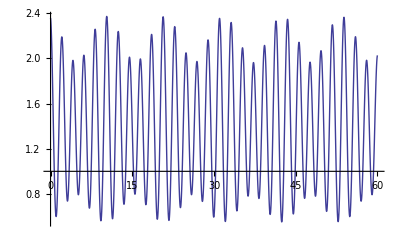

```mathematica
Fig1=Plot[ExpectedA[t],{t,0,60}]
```

#### Density matrix:

```mathematica
Subscript[ρ, 0]=ComplexExpand[Subscript[ψ, 0].Conjugate[Transpose[Subscript[ψ, 0]]]]//Chop
```

{{0.405666,0.438709+0.0826048 ⅈ,0.187465-0.0816608 ⅈ},{0.438709-0.0826048 ⅈ,0.491264,0.186107-0.126486 ⅈ},{0.187465+0.0816608 ⅈ,0.186107+0.126486 ⅈ,0.103069}}

```mathematica
MatrixForm[Subscript[ρ, 0]]
```

(0.405666 | 0.438709+0.0826048 ⅈ | 0.187465-0.0816608 ⅈ
0.438709-0.0826048 ⅈ | 0.491264 | 0.186107-0.126486 ⅈ
0.187465+0.0816608 ⅈ | 0.186107+0.126486 ⅈ | 0.103069)

```mathematica
Tr[Subscript[ρ, 0]]
```

1.

```mathematica
ρ[t_]:=ComplexExpand[State[t].Conjugate[Transpose[State[t]]]]//Chop
```

```mathematica
ρ[0]
```

{{0.405666,0.438709+0.0826048 ⅈ,0.187465-0.0816608 ⅈ},{0.438709-0.0826048 ⅈ,0.491264,0.186107-0.126486 ⅈ},{0.187465+0.0816608 ⅈ,0.186107+0.126486 ⅈ,0.103069}}

```mathematica
Tr[ρ[t]]//Simplify//Chop
```

1.

```mathematica
Tr[𝔸.ρ[t]]//Simplify//Chop
```

1.4206+0.040631 Cos[0.582784 t]+0.160311 Cos[2.44846 t]+0.734818 Cos[3.03125 t]-0.00847146 Sin[0.582784 t]+0.0313462 Sin[2.44846 t]-0.126827 Sin[3.03125 t]

```mathematica
Fig2=Plot[1.4206041895790176+0.04063095136927784 Cos[0.5827840921930183 t]+0.1603105206830209 Cos[2.4484646760748454 t]+0.734818245707444 Cos[3.0312487682678637 t]-0.0084714644211495 Sin[0.5827840921930183 t]+0.03134617643494404 Sin[2.4484646760748454 t]-0.12682693134008766 Sin[3.0312487682678637 t],{t,0,60}]
```

-Graphics-

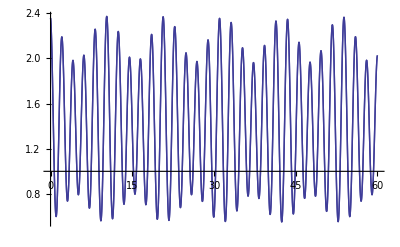

```mathematica
Show[Fig1, Fig2]
```

#### We kill the off-diagonal elements (which is to say: all the interference terms)

```mathematica
?Diagonal
```

Diagonal[m] gives the list of elements on the leading diagonal of the matrix m.
Diagonal[m,k] gives the elements on the k^th diagonal of m.

```mathematica
Diagonal[Subscript[ρ, 0]]
```

{0.405666,0.491264,0.103069}

```mathematica
({{a1, a2, a3}, {b1, b2, b3}, {c1, c2, c3}})
```

{{a1,a2,a3},{b1,b2,b3},{c1,c2,c3}}

```mathematica
{{Diagonal[Subscript[ρ, 0]]⟦1⟧,0,0},{0,Diagonal[Subscript[ρ, 0]]⟦2⟧,0},{0,0,Diagonal[Subscript[ρ, 0]]⟦3⟧}}//MatrixForm
```

(0.405666 | 0 | 0
0 | 0.491264 | 0
0 | 0 | 0.103069)

```mathematica
R[t_]:={{Diagonal[ρ[t]]⟦1⟧,0,0},{0,Diagonal[ρ[t]]⟦2⟧,0},{0,0,Diagonal[ρ[t]]⟦3⟧}}
```

```mathematica
Tr[𝔸.R[t]]//Simplify//Chop
```

0.63081+0.0398669 Cos[0.582784 t]+0.141821 Cos[2.44846 t]+0.0962767 Cos[3.03125 t]-0.0470452 Sin[0.582784 t]-0.0385905 Sin[2.44846 t]-0.11754 Sin[3.03125 t]

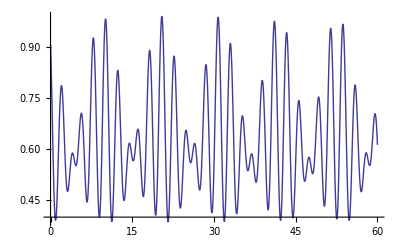

```mathematica
Plot[0.6308099912082596+0.03986687415676307 Cos[0.5827840921930183 t]+0.14182107817986891 Cos[2.4484646760748454 t]+0.09627668554402627 Cos[3.0312487682678637 t]-0.04704522650676235 Sin[0.5827840921930183 t]-0.03859053009749735 Sin[2.4484646760748454 t]-0.1175399614770487 Sin[3.0312487682678637 t],{t,0,60}]
```

```mathematica
R1[t_]:={{Diagonal[ρ[t]]⟦1⟧,0,0},{0,0,0},{0,0,0}}
R2[t_]:={{0,0,0},{0,Diagonal[ρ[t]]⟦2⟧,0},{0,0,0}}
R3[t_]:={{0,0,0},{0,0,0},{0,0,Diagonal[ρ[t]]⟦3⟧}}
```

```mathematica
f1[t_]:=Tr[𝔸.R1[t]]//Simplify//Chop
f2[t_]:=Tr[𝔸.R2[t]]//Simplify//Chop
f3[t_]:=Tr[𝔸.R3[t]]//Simplify//Chop
```

```mathematica
f1[t]
```

0.204811-0.000793328 Cos[0.582784 t]-0.0138633 Cos[2.44846 t]-0.0346407 Cos[3.03125 t]-0.0051189 Sin[0.582784 t]-0.00646395 Sin[2.44846 t]+0.119325 Sin[3.03125 t]

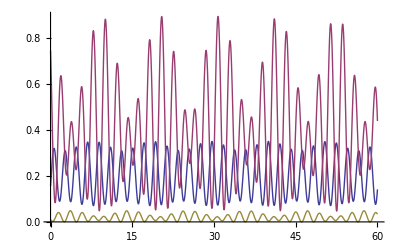

```mathematica
Plot[Evaluate[{f1[t],f2[t],f3[t]}],{t,0,60}]
```

```mathematica
Plot[Evaluate[{f1[t]+f2[t]+f3[t]}],{t,0,60}]
```

-Graphics-